## Лабораторная работа № 1. Задача Сода. Вариант № 1, Баталов С. А.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\BSA\Documents\University_SPbU\Magistracy_Degree\Subjects\Multiphase_Flows\LVP\Reports\Report_1

### Импорт численного решения

```mathematica
data = {{Import["0\\data1000.csv"][[2;;-1]], Import["0.1\\data100.csv"][[2;;-1]], Import["0.2\\data100.csv"][[2;;-1]]},
		{Import["0\\data1000.csv"][[2;;-1]], Import["0.1\\data1000.csv"][[2;;-1]], Import["0.2\\data1000.csv"][[2;;-1]]}};
xv[v_, i_, j_] := data[[i, j, All, {1, If[v == "p", 4, If[v == "ρ", 3, 2]]}]];
```

### Построение графиков

```mathematica
PlotSod[v_, j_] := ListLinePlot[{xv[v, 1, j], xv[v, 2, j]}, PlotLegends -> Placed[{"n = 100", "n = 1000"}, {Left, Bottom}], 
	GridLines -> Automatic, AxesLabel -> {x, v}, ImageSize -> Scaled[1], PlotStyle -> {Darker[Green], {Blue, Dashed}, PlotRange -> All},
	PlotLabel->Style[If[j == 1, "t = 0", If[j == 2, "t = 0.1", "t = 0.2"]], Italic]];
```

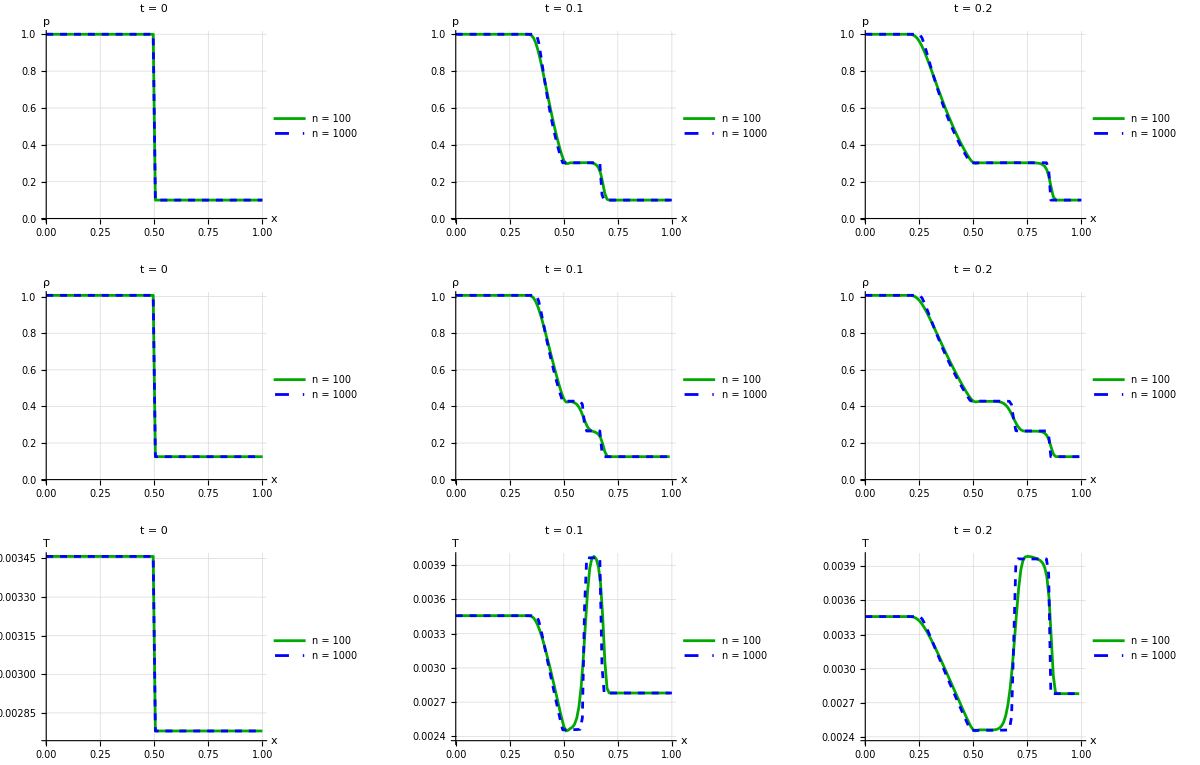

```mathematica
GraphicsGrid[{{PlotSod["p", 1], PlotSod["p", 2], PlotSod["p", 3]},
			{PlotSod["ρ", 1], PlotSod["ρ", 2], PlotSod["ρ", 3]},
			{PlotSod["T", 1], PlotSod["T", 2], PlotSod["T", 3]}}, ImageSize -> Scaled[1]]
```

### Выводы

В пакете OpenFOAM была численно решена задача Сода. Использовался встроенный решатель shockFluid. В процессе было обнаружено, что исходные файлы лабораторной работы устарели, была произведена их доработка. Искомые файлы находятся в соответствующем репозитории проекта.

Задача Сода была решена с различной степенью точности, на графиках представлены распределения макропараметров для двух расчетных сеток: n = 100 и n = 1000, нетрудно заметить, что для более плотной сетки численное решение более точно соответствует исходному аналитическому решению задачи, хотя последнее в данной работе не приводится.

Основными результатами данной работы можно считать: успешное ознакомление студента с основами работы в прикладном пакете программ OpenFOAM, успешную доработку исходных файлов лабораторной работы.